```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
SetDirectory["/home/dan/ResearchLocal/adiabatic/athena4.2_jake2/bin/"];
```

```mathematica
data1=Import["am4.txt", "Data"];
data2=Import["am5.txt", "Data"];
data3=Import["am6.txt", "Data"];
```

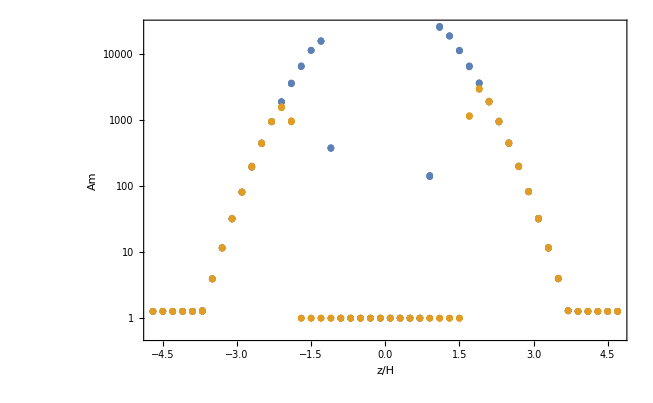

```mathematica
ListLogPlot[{
Transpose[{data1[[All,2]],data1[[All,3]]}],
Transpose[{data2[[All,2]],data2[[All,3]]}]
}
,Frame->True,FrameLabel->{"z/H","Am"}]
```

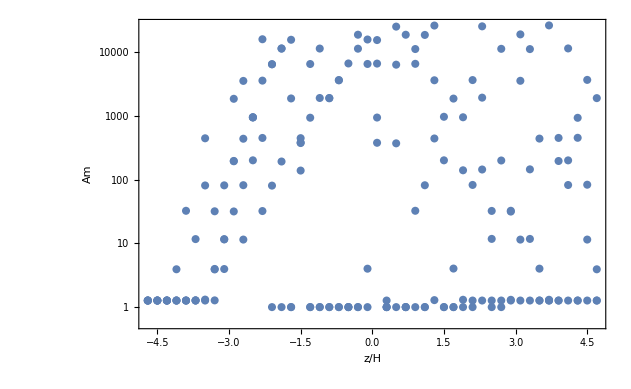

```mathematica
ListLogPlot[Transpose[{data3[[All,2]],data1[[All,3]]}],Frame->True,FrameLabel->{"z/H","Am"}]
```